```mathematica
ωr=2π 10.0;
Subscript[ωq, i_]:=2π{5.0,6.0,7.0,8.0,11.0,12.0,13.0,14.0}[[i+1]];
ωqswap=2π 9.0;
Subscript[g, i_]:=2π{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}[[i+1]];
Subscript[Δ, i_]:=Subscript[ωq, i]-ωr;
```

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
Id=PauliMatrix[0];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
σp=ket1.ket0†;
σm=ket0.ket1†;
QopAsc[i_,j_,qop_]:=<|Mod[i+0,8]->qop,Mod[i+1,8]->Id,Mod[i+2,8]->Id,Mod[i+3,8]->Id,Mod[i+4,8]->Id,Mod[i+5,8]->Id,Mod[i+6,8]->Id,Mod[i+7,8]->Id|>[j];
Subscript[Id, i_]:=KroneckerProduct[QopAsc[i,0,Id],QopAsc[i,1,Id],QopAsc[i,2,Id],QopAsc[i,3,Id],QopAsc[i,4,Id],QopAsc[i,5,Id],QopAsc[i,6,Id],QopAsc[i,7,Id]];
Subscript[σx, i_]:=KroneckerProduct[QopAsc[i,0,σx],QopAsc[i,1,σx],QopAsc[i,2,σx],QopAsc[i,3,σx],QopAsc[i,4,σx],QopAsc[i,5,σx],QopAsc[i,6,σx],QopAsc[i,7,σx]];
Subscript[σy, i_]:=KroneckerProduct[QopAsc[i,0,σy],QopAsc[i,1,σy],QopAsc[i,2,σy],QopAsc[i,3,σy],QopAsc[i,4,σy],QopAsc[i,5,σy],QopAsc[i,6,σy],QopAsc[i,7,σy]];
Subscript[σz, i_]:=KroneckerProduct[QopAsc[i,0,σz],QopAsc[i,1,σz],QopAsc[i,2,σz],QopAsc[i,3,σz],QopAsc[i,4,σz],QopAsc[i,5,σz],QopAsc[i,6,σz],QopAsc[i,7,σz]];
Subscript[σp, i_]:=KroneckerProduct[QopAsc[i,0,σp],QopAsc[i,1,σp],QopAsc[i,2,σp],QopAsc[i,3,σp],QopAsc[i,4,σp],QopAsc[i,5,σp],QopAsc[i,6,σp],QopAsc[i,7,σp]];
Subscript[σm, i_]:=KroneckerProduct[QopAsc[i,0,σm],QopAsc[i,1,σm],QopAsc[i,2,σm],QopAsc[i,3,σm],QopAsc[i,4,σm],QopAsc[i,5,σm],QopAsc[i,6,σm],QopAsc[i,7,σm]];
```

```mathematica
Rx[target_,θ_]:=MatrixExp[-ⅈ θ Subscript[σx, target] /2];
Ry[target_,θ_]:=MatrixExp[-ⅈ θ Subscript[σy, target] /2];
```

```mathematica
GaussianPulse[x_,ts_,tf_]:=(UnitStep[x-μ+3σ]-UnitStep[x-μ-3σ])PDF[NormalDistribution[μ,σ],x]/0.997300204/.{μ->(tf+ts)/2,σ->(tf-ts)/6};
SquarePulse[x_,ts_,tf_]:=(UnitStep[x-μ+3σ]-UnitStep[x-μ-3σ])/(6σ)/.{μ->(tf+ts)/2,σ->(tf-ts)/6};
```

```mathematica
Rx[target_,θ_]:=Module[{H:=-1/2 Sum[(Subscript[ωq, i]-Subscript[ωq, target])Subscript[σz, i],{i,0,3}]},
H=H+1/2 θ GaussianPulse[t,0,10] Subscript[σx, target];
MatrixExp[-ⅈ NIntegrate[H,{t,0,10}]]
];
Ry[target_,θ_]:=Module[{H:=-1/2 Sum[(Subscript[ωq, i]-Subscript[ωq, target])Subscript[σz, i],{i,0,3}]},
H=H+1/2 θ GaussianPulse[t,0,10] Subscript[σy, target];
MatrixExp[-ⅈ NIntegrate[H,{t,0,10}]]
];
```

```mathematica
sqrtiSWAP[target1_,target2_]:=Module[{H=-1/2 Sum[Subscript[ωq, i] Subscript[σz, i],{i,0,3}]+Sum[(Subscript[g, i] Subscript[g, j]/Subscript[Δ, i])(Subscript[σp, i] .Subscript[σm, j]+Subscript[σm, i] .Subscript[σp, j])/2,{i,0,3},{j,0,3}],J=0,Δswap=ωqswap-ωr},
H=H+1/2(Subscript[ωq, target1] Subscript[σz, target1]+Subscript[ωq, target2] Subscript[σz, target2])-Subscript[g, target1] Subscript[g, target2] (Subscript[Δ, target1]+Subscript[Δ, target2])/(Subscript[Δ, target1] Subscript[Δ, target2])(Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/2;
H=H-1/2 ωqswap(Subscript[σz, target1]+Subscript[σz, target2])+Subscript[g, target1] Subscript[g, target2] (Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/Δswap;
H=Subscript[g, target1] Subscript[g, target2] (Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/Δswap;
J=Abs[Subscript[g, target1] Subscript[g, target2] /Δswap];
MatrixExp[-ⅈ H π/(4 J)]
];
iSWAP[target1_,target2_]:=Module[{H=-1/2 Sum[Subscript[ωq, i] Subscript[σz, i],{i,0,3}]+Sum[(Subscript[g, i] Subscript[g, j]/Subscript[Δ, i])(Subscript[σp, i] .Subscript[σm, j]+Subscript[σm, i] .Subscript[σp, j])/2,{i,0,3},{j,0,3}],J=0,Δswap=ωqswap-ωr},
H=H+1/2(Subscript[ωq, target1] Subscript[σz, target1]+Subscript[ωq, target2] Subscript[σz, target2])-Subscript[g, target1] Subscript[g, target2] (Subscript[Δ, target1]+Subscript[Δ, target2])/(Subscript[Δ, target1] Subscript[Δ, target2])(Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/2;
H=H-1/2 ωqswap(Subscript[σz, target1]+Subscript[σz, target2])+Subscript[g, target1] Subscript[g, target2] (Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/Δswap;
H=Subscript[g, target1] Subscript[g, target2] (Subscript[σp, target1] .Subscript[σm, target2]+Subscript[σm, target1] .Subscript[σp, target2])/Δswap;
J=Abs[Subscript[g, target1] Subscript[g, target2] /Δswap];
MatrixExp[-ⅈ H π/(2 J)]
];
```

```mathematica
X[target_]:=Rx[target, π]//FullSimplify;
Y[target_]:=Ry[target, π]//FullSimplify;
Rz[target_,θ_]:=Ry[target,-π/2].Rx[target,θ].Ry[target,π/2]//FullSimplify;
Z[target_]:=Rz[target,π]//FullSimplify;
H[target_]:=X[target].Ry[target,π/2]//FullSimplify;
CNOT[control_,target_]:=Rx[target,π/2].iSWAP[control,target].Rx[control,π/2].iSWAP[control,target].Rx[target,π/2].iSWAP[control,target].H[control].iSWAP[control,target].Rz[control,-π/2].Rz[target,-π/2].H[target]//FullSimplify;
CRy[control_,target_,θ_]:=CNOT[control,target].Ry[target,-θ/2].CNOT[control,target].Ry[target,θ/2]//FullSimplify;
CRz[control_,target_,θ_]:=CNOT[control,target].Rz[target,-θ/2].CNOT[control,target].Rz[target,θ/2]//FullSimplify;
SWAP[target1_,target2_]:=CNOT[target1,target2].CNOT[target2,target1].CNOT[target1,target2]//FullSimplify;
CH[control_,target_]:=Ry[target,-π/4].CNOT[control,target].Ry[target,π/4]//FullSimplify;
CP00[control_,target_,θ_]:=CRz[target,control,θ/2].CRz[control,target,θ/2].Rz[target,-3 θ/4].Rz[control,-3 θ/4]//FullSimplify;
CP01[control_,target_,θ_]:=CRz[target,control,θ/2].CRz[control,target,-3 θ/2].Rz[target,5 θ/4].Rz[control,-3 θ/4]//FullSimplify;
CP10[control_,target_,θ_]:=CRz[target,control,θ/2].CRz[control,target,-3 θ/2].Rz[target,θ/4].Rz[control,θ/4]//FullSimplify;
CP11[control_,target_,θ_]:=CRz[target,control,θ/2].CRz[control,target,θ/2].Rz[target,θ/4].Rz[control,θ/4]//FullSimplify;
Toffoli[control1_,control2_,target_]:=CP11[control1,control2,-π/2].H[target].CRz[control1,target,-π/2].CNOT[control1,control2].CRz[control2,target,π/2].CNOT[control1,control2].CRz[control2,target,-π/2].H[target]//FullSimplify;
CCRz[control1_,control2_,target_,θ_]:=CRz[control1,target,θ/2].CNOT[control1,control2].CRz[control2,target,-θ/2].CNOT[control1,control2].CRz[control2,target,θ/2]//FullSimplify;
CCRy[control1_,control2_,target_,θ_]:=CRy[control1,target,θ/2].CNOT[control1,control2].CRy[control2,target,-θ/2].CNOT[control1,control2].CRy[control2,target,θ/2]//FullSimplify;
CCNOT[control1_,control2_,target_]:=Toffoli[control1,control2,target]//FullSimplify;
CCP00[control1_,control2_,target_,θ_]:=CP00[control1,target,θ/2].X[control1].CNOT[control1,control2].X[control1].CP00[control2,target,-θ/2].X[control1].CNOT[control1,control2].X[control1].CP00[control2,target,θ/2]//FullSimplify;
CCP01[control1_,control2_,target_,θ_]:=CP01[control1,target,θ/2].X[control1].CNOT[control1,control2].X[control1].CP01[control2,target,-θ/2].X[control1].CNOT[control1,control2].X[control1].CP01[control2,target,θ/2]//FullSimplify;
CCP10[control1_,control2_,target_,θ_]:=CP10[control1,target,θ/2].CNOT[control1,control2].CP10[control2,target,-θ/2].CNOT[control1,control2].CP10[control2,target,θ/2]//FullSimplify;
CCP11[control1_,control2_,target_,θ_]:=CP11[control1,target,θ/2].CNOT[control1,control2].CP11[control2,target,-θ/2].CNOT[control1,control2].CP11[control2,target,θ/2]//FullSimplify;
mZ[target_]:=X[target].Y[target]//FullSimplify;
CCCNOT[control1_,control2_,control3_,target_]:=CP11[control1,control3,-π/4].CNOT[control1,control2].CP11[control2,control3,π/4].CNOT[control1,control2].CP11[control2,control3,-π/4].H[target].CCRz[control1,control3,target,-π/2].CNOT[control1,control2].CCRz[control2,control3,target,π/2].CNOT[control1,control2].CCRz[control2,control3,target,-π/2].H[target]//FullSimplify;
CCCRy[control1_,control2_,control3_,target_,θ_]:=CCRy[control1,control2,target,θ/2].CCNOT[control1,control2,control3].CRy[control3,target,-θ/2].CCNOT[control1,control2,control3].CRy[control3,target,θ/2]//FullSimplify;
CCCRz[control1_,control2_,control3_,target_,θ_]:=CCRz[control1,control2,target,θ/2].CCNOT[control1,control2,control3].CRz[control3,target,-θ/2].CCNOT[control1,control2,control3].CRz[control3,target,θ/2]//FullSimplify;
CCCP00[control1_,control2_,control3_,target_,θ_]:=CCP00[control1,control2,target,θ/2].X[control1].X[control2].CCNOT[control1,control2,control3].X[control1].X[control2].CP00[control3,target,-θ/2].X[control1].X[control2].CCNOT[control1,control2,control3].X[control1].X[control2].CP00[control3,target,θ/2]//FullSimplify;
CCCP01[control1_,control2_,control3_,target_,θ_]:=CCP01[control1,control2,target,θ/2].X[control1].X[control2].CCNOT[control1,control2,control3].X[control1].X[control2].CP01[control3,target,-θ/2].X[control1].X[control2].CCNOT[control1,control2,control3].X[control1].X[control2].CP01[control3,target,θ/2]//FullSimplify;
CCCP10[control1_,control2_,control3_,target_,θ_]:=CCP10[control1,control2,target,θ/2].CCNOT[control1,control2,control3].CP10[control3,target,-θ/2].CCNOT[control1,control2,control3].CP10[control3,target,θ/2]//FullSimplify;
CCCP11[control1_,control2_,control3_,target_,θ_]:=CCP11[control1,control2,target,θ/2].CCNOT[control1,control2,control3].CP11[control3,target,-θ/2].CCNOT[control1,control2,control3].CP11[control3,target,θ/2]//FullSimplify;
CCCCNOT[control1_,control2_,control3_,control4_,target_]:=CCCP11[control1,control2,control3,control4,-π/2].H[target].CCCRz[control1,control3,control4,target,-π/2].CNOT[control1,control2].CCCRz[control2,control3,control4,target,π/2].CNOT[control1,control2].CCCRz[control2,control3,control4,target,-π/2].H[target]//FullSimplify;
```

```mathematica
(*Shor*)
QFT4d[target1_,target2_,target3_,target4_]:=H[target1].CP11[target2,target1,-2 π/2^2].CP11[target3,target1,-2 π/2^3].CP11[target4,target1,-2 π/2^4].H[target2].CP11[target3,target2,-2 π/2^2].CP11[target4,target2,-2 π/2^3].H[target3].CP11[target4,target3,-2 π/2^2].H[target4].SWAP[target1,target4].SWAP[target2,target3];
CMUL3[control_,target1_,target2_,target3_,target4_]:=CNOT[control,target1].CCCNOT[control,target1,target4,target3].CCNOT[control,target1,target4].CCCCNOT[control,target1,target4,target3,target2].CCNOT[control,target1,target4].CNOT[control,target1];
```

```mathematica
ketpsi=KroneckerProduct[ket0,ket0,ket0,ket0,ket0,ket0,ket0,ket0];

ketpsi=X[7].ketpsi;

ketpsi=H[0].ketpsi;
ketpsi=H[1].ketpsi;
ketpsi=H[2].ketpsi;
ketpsi=H[3].ketpsi;

(*U3=CMUL3[3,4,5,6,7];*)
ketpsi=U3.ketpsi;

(*U2=CMUL3[2,4,5,6,7];*)
ketpsi=U2.ketpsi;
ketpsi=U2.ketpsi;

(*U1=CMUL3[1,4,5,6,7];*)
ketpsi=U1.ketpsi;
ketpsi=U1.ketpsi;
ketpsi=U1.ketpsi;
ketpsi=U1.ketpsi;

(*U0=CMUL3[0,4,5,6,7];*)
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;
ketpsi=U0.ketpsi;

ketpsi=QFT4d[0,1,2,3].ketpsi;
```

```mathematica
ketpsi
```

{{-5.12619×10^-14+7.44175×10^-14 ⅈ},{0.415735+0.277785 ⅈ},{-5.13819×10^-15+4.78393×10^-14 ⅈ},{0.415735+0.277785 ⅈ},{-1.52077×10^-15+6.38926×10^-15 ⅈ},{4.20813×10^-16+6.03187×10^-15 ⅈ},{2.04599×10^-15+1.92819×10^-14 ⅈ},{-7.17106×10^-17+1.43602×10^-15 ⅈ},{-4.08989×10^-14+3.90878×10^-14 ⅈ},{-3.52829×10^-14+3.8621×10^-14 ⅈ},{-2.93588×10^-14+3.0313×10^-14 ⅈ},{-2.67688×10^-14+3.25143×10^-14 ⅈ},{4.60522×10^-16+2.67812×10^-15 ⅈ},{5.53534×10^-16+1.38051×10^-15 ⅈ},{1.62955×10^-15+1.01823×10^-15 ⅈ},{-5.39808×10^-16-1.3478×10^-15 ⅈ},{2.88889×10^-15-2.58092×10^-15 ⅈ},{2.40141×10^-15+5.05249×10^-15 ⅈ},{5.82687×10^-15+3.63746×10^-15 ⅈ},{4.81039×10^-15+2.07473×10^-15 ⅈ},{1.15562×10^-15-7.03359×10^-16 ⅈ},{7.81665×10^-16-1.64313×10^-16 ⅈ},{-3.5866×10^-15-1.0459×10^-15 ⅈ},{-8.75376×10^-16-2.57395×10^-16 ⅈ},{-7.35991×10^-17-3.58027×10^-15 ⅈ},{1.14611×10^-16-2.44582×10^-15 ⅈ},{3.60734×10^-16-3.13145×10^-15 ⅈ},{-2.6916×10^-16-2.08424×10^-15 ⅈ},{-1.51922×10^-16-8.09469×10^-17 ⅈ},{-4.39442×10^-16+1.41491×10^-16 ⅈ},{-5.83595×10^-17+6.63021×10^-17 ⅈ},{7.23637×10^-16-2.20962×10^-15 ⅈ},{1.22878×10^-15-1.29362×10^-16 ⅈ},{4.2134×10^-17+3.49439×10^-15 ⅈ},{2.73122×10^-15+2.4215×10^-15 ⅈ},{2.87964×10^-15+9.50628×10^-16 ⅈ},{6.03643×10^-16-5.63466×10^-17 ⅈ},{4.37385×10^-16-9.65963×10^-17 ⅈ},{-1.67722×10^-15-8.83412×10^-16 ⅈ},{-3.94703×10^-16-2.97415×10^-16 ⅈ},{2.22208×10^-16-1.63705×10^-15 ⅈ},{4.55145×10^-16-1.14275×10^-15 ⅈ},{5.71454×10^-16-1.69502×10^-15 ⅈ},{-8.1077×10^-17-1.1168×10^-15 ⅈ},{-6.42649×10^-17-5.89776×10^-17 ⅈ},{-2.32669×10^-16+1.56119×10^-17 ⅈ},{-3.78427×10^-17+2.28157×10^-17 ⅈ},{5.41038×10^-16-1.11892×10^-15 ⅈ},{3.326×10^-16+6.99169×10^-16 ⅈ},{-7.59669×10^-16+2.5631×10^-15 ⅈ},{1.65915×10^-15+2.04993×10^-15 ⅈ},{2.41127×10^-15+2.58474×10^-16 ⅈ},{3.51622×10^-16+1.79817×10^-16 ⅈ},{3.47155×10^-16-7.51523×10^-17 ⅈ},{-1.00417×10^-15-8.23274×10^-16 ⅈ},{-1.99887×10^-16-3.16282×10^-16 ⅈ},{2.67324×10^-16-9.63657×10^-16 ⅈ},{5.73341×10^-16-6.3156×10^-16 ⅈ},{7.0349×10^-16-1.18733×10^-15 ⅈ},{-1.96552×10^-17-8.27938×10^-16 ⅈ},{-3.20474×10^-17-5.06071×10^-17 ⅈ},{-1.56577×10^-16-2.96485×10^-17 ⅈ},{-2.9562×10^-17+6.38961×10^-18 ⅈ},{4.97212×10^-16-7.58235×10^-16 ⅈ},{-4.93766×10^-16+1.11232×10^-15 ⅈ},{-1.90766×10^-15+2.20125×10^-15 ⅈ},{1.09526×10^-15+1.90922×10^-15 ⅈ},{2.56045×10^-15+2.08167×10^-16 ⅈ},{1.51814×10^-16+3.17395×10^-16 ⅈ},{3.3174×10^-16-6.60915×10^-17 ⅈ},{-6.3713×10^-16-7.87374×10^-16 ⅈ},{-6.60915×10^-17-3.3174×10^-16 ⅈ},{2.27707×10^-16-6.08996×10^-16 ⅈ},{6.35801×10^-16-2.96471×10^-16 ⅈ},{8.382×10^-16-9.08983×10^-16 ⅈ},{8.54642×10^-18-7.27029×10^-16 ⅈ},{-1.3046×10^-17-4.53623×10^-17 ⅈ},{-1.11599×10^-16-5.52956×10^-17 ⅈ},{-2.39077×10^-17-3.75954×10^-18 ⅈ},{4.95609×10^-16-5.87355×10^-16 ⅈ},{-1.52867×10^-15+1.33854×10^-15 ⅈ},{-2.57184×10^-15+1.57568×10^-15 ⅈ},{7.41557×10^-16+1.90061×10^-15 ⅈ},{2.89352×10^-15+3.79904×10^-16 ⅈ},{-7.13765×10^-17+4.23135×10^-16 ⅈ},{3.687×10^-16-6.36359×10^-17 ⅈ},{-3.87932×10^-16-7.58644×10^-16 ⅈ},{6.34186×10^-17-3.49489×10^-16 ⅈ},{1.10679×10^-16-3.85846×10^-16 ⅈ},{6.75403×10^-16+1.00665×10^-17 ⅈ},{1.01766×10^-15-7.1793×10^-16 ⅈ},{2.02631×10^-17-7.37982×10^-16 ⅈ},{1.86434×10^-18-4.0847×10^-17 ⅈ},{-7.61773×10^-17-7.40621×10^-17 ⅈ},{-1.84711×10^-17-1.23221×10^-17 ⅈ},{5.25816×10^-16-5.07573×10^-16 ⅈ},{-3.26473×10^-15+1.41421×10^-15 ⅈ},{-4.02044×10^-15+9.88859×10^-16 ⅈ},{5.15963×10^-16+2.06101×10^-15 ⅈ},{4.23273×10^-15+5.82867×10^-16 ⅈ},{-4.17566×10^-16+5.31075×10^-16 ⅈ},{4.89401×10^-16-6.8793×10^-17 ⅈ},{-1.89486×10^-16-7.27379×10^-16 ⅈ},{2.40974×10^-16-3.77582×10^-16 ⅈ},{-1.55967×10^-16-2.42092×10^-16 ⅈ},{7.01545×10^-16+4.0627×10^-16 ⅈ},{1.32994×10^-15-5.61795×10^-16 ⅈ},{1.52944×10^-17-8.99629×10^-16 ⅈ},{1.76053×10^-17-3.54146×10^-17 ⅈ},{-3.85677×10^-17-9.16119×10^-17 ⅈ},{-1.10669×10^-17-2.23583×10^-17 ⅈ},{6.10095×10^-16-5.13768×10^-16 ⅈ},{-7.95941×10^-15+1.14559×10^-15 ⅈ},{-7.64237×10^-15-6.45177×10^-16 ⅈ},{4.78761×10^-16+2.76714×10^-15 ⅈ},{8.00228×10^-15+1.65493×10^-15 ⅈ},{-1.30979×10^-15+7.14804×10^-16 ⅈ},{9.07243×10^-16-9.71896×10^-17 ⅈ},{5.10322×10^-18-6.6921×10^-16 ⅈ},{6.59284×10^-16-4.50935×10^-16 ⅈ},{-9.86594×10^-16-2.12538×10^-16 ⅈ},{7.09474×10^-16+1.29386×10^-15 ⅈ},{2.19187×10^-15-3.95596×10^-16 ⅈ},{-3.64992×10^-17-1.55994×10^-15 ⅈ},{4.57304×10^-17-2.40609×10^-17 ⅈ},{2.9161×10^-17-1.1737×10^-16 ⅈ},{6.28305×10^-18-4.27576×10^-17 ⅈ},{8.90357×10^-16-7.48652×10^-16 ⅈ},{-8.74705×10^-15+3.59776×10^-14 ⅈ},{0.415735+0.277785 ⅈ},{6.58385×10^-15-3.01135×10^-15 ⅈ},{-0.415735-0.277785 ⅈ},{1.10096×10^-15+5.02394×10^-15 ⅈ},{-2.52409×10^-15-7.39606×10^-15 ⅈ},{-1.09761×10^-15-9.27371×10^-15 ⅈ},{1.93998×10^-15+2.97156×10^-15 ⅈ},{-7.81328×10^-15+6.10361×10^-15 ⅈ},{-1.03997×10^-14+1.62705×10^-14 ⅈ},{8.4551×10^-15-8.22021×10^-15 ⅈ},{1.04446×10^-14-1.30809×10^-14 ⅈ},{-5.55207×10^-17+9.24408×10^-17 ⅈ},{3.21322×10^-17+1.79933×10^-16 ⅈ},{6.25356×10^-17+9.00746×10^-17 ⅈ},{1.54108×10^-16-3.10372×10^-16 ⅈ},{9.50298×10^-15+3.34793×10^-15 ⅈ},{5.39444×10^-15+5.22054×10^-15 ⅈ},{-8.39259×10^-16-5.51876×10^-16 ⅈ},{-8.08381×10^-15-3.35149×10^-15 ⅈ},{1.89721×10^-15+3.06406×10^-16 ⅈ},{-8.7944×10^-16+4.51734×10^-17 ⅈ},{1.50929×10^-16-8.18524×10^-16 ⅈ},{-7.39451×10^-16-1.84742×10^-16 ⅈ},{2.38156×10^-15+5.90713×10^-16 ⅈ},{8.39551×10^-16-1.54026×10^-15 ⅈ},{-1.05864×10^-15-3.62886×10^-16 ⅈ},{2.53671×10^-16+1.46357×10^-15 ⅈ},{-2.21674×10^-17-5.78094×10^-17 ⅈ},{-1.36385×10^-16-7.67319×10^-17 ⅈ},{-5.14571×10^-17+1.59818×10^-17 ⅈ},{-2.85205×10^-16+6.79594×10^-16 ⅈ},{4.8083×10^-15+3.07931×10^-15 ⅈ},{1.8279×10^-15+3.4315×10^-15 ⅈ},{-8.76461×10^-16+1.54255×10^-16 ⅈ},{-4.33334×10^-15-2.17187×10^-15 ⅈ},{1.00499×10^-15+4.90134×10^-16 ⅈ},{-4.61598×10^-16+1.67768×10^-17 ⅈ},{3.45518×10^-16-7.60354×10^-16 ⅈ},{-3.21141×10^-16-2.58095×10^-16 ⅈ},{1.55093×10^-15+6.20267×10^-16 ⅈ},{8.47479×10^-16-6.5267×10^-16 ⅈ},{-1.96707×10^-16-1.96687×10^-16 ⅈ},{2.01877×10^-16+8.03257×10^-16 ⅈ},{5.95766×10^-18-4.64556×10^-17 ⅈ},{-6.86561×10^-17-1.0249×10^-16 ⅈ},{-3.41071×10^-17-4.41746×10^-18 ⅈ},{-4.94387×10^-18+4.4471×10^-16 ⅈ},{3.07224×10^-15+3.15498×10^-15 ⅈ},{3.7456×10^-16+2.70699×10^-15 ⅈ},{-1.10205×10^-15+3.14653×10^-16 ⅈ},{-2.94556×10^-15-1.62544×10^-15 ⅈ},{6.58799×10^-16+5.98075×10^-16 ⅈ},{-3.40897×10^-16+1.16196×10^-17 ⅈ},{5.43965×10^-16-7.2909×10^-16 ⅈ},{-1.43585×10^-16-2.86188×10^-16 ⅈ},{1.28428×10^-15+7.64021×10^-16 ⅈ},{8.73621×10^-16-2.56466×10^-16 ⅈ},{1.15565×10^-16-4.05517×10^-17 ⅈ},{1.96909×10^-16+6.41611×10^-16 ⅈ},{2.16986×10^-17-4.10232×10^-17 ⅈ},{-3.10465×10^-17-1.2004×10^-16 ⅈ},{-2.67029×10^-17-1.44537×10^-17 ⅈ},{7.93353×10^-17+4.38515×10^-16 ⅈ},{2.03734×10^-15+3.38119×10^-15 ⅈ},{-5.96849×10^-16+2.0705×10^-15 ⅈ},{-1.45576×10^-15+3.06037×10^-16 ⅈ},{-2.56305×10^-15-1.53957×10^-15 ⅈ},{4.35608×10^-16+7.03815×10^-16 ⅈ},{-3.03937×10^-16+1.40753×10^-17 ⅈ},{7.93162×10^-16-7.00359×10^-16 ⅈ},{-1.40753×10^-17-3.03937×10^-16 ⅈ},{1.16725×10^-15+9.87171×10^-16 ⅈ},{9.13223×10^-16+5.00708×10^-17 ⅈ},{2.95028×10^-16+1.50501×10^-16 ⅈ},{2.08625×10^-16+6.30657×10^-16 ⅈ},{3.66089×10^-17-3.65079×10^-17 ⅈ},{4.37556×10^-18-1.38806×10^-16 ⅈ},{-2.12663×10^-17-2.30163×10^-17 ⅈ},{1.09542×10^-16+5.18298×10^-16 ⅈ},{1.21097×10^-15+3.79435×10^-15 ⅈ},{-1.44231×10^-15+1.72723×10^-15 ⅈ},{-2.01965×10^-15+1.6533×10^-16 ⅈ},{-2.36269×10^-15-1.78156×10^-15 ⅈ},{2.358×10^-16+8.41393×10^-16 ⅈ},{-3.19351×10^-16+2.31361×10^-17 ⅈ},{1.1602×10^-15-6.64459×10^-16 ⅈ},{1.19721×10^-16-3.19395×10^-16 ⅈ},{1.12764×10^-15+1.34183×10^-15 ⅈ},{9.75683×10^-16+3.8516×10^-16 ⅈ},{4.29738×10^-16+4.28847×10^-16 ⅈ},{2.36827×10^-16+7.31566×10^-16 ⅈ},{5.56104×10^-17-3.12631×10^-17 ⅈ},{4.9353×10^-17-1.64453×10^-16 ⅈ},{-1.5612×10^-17-3.31654×10^-17 ⅈ},{1.0794×10^-16+6.89177×10^-16 ⅈ},{3.14786×10^-16+4.62288×10^-15 ⅈ},{-2.58452×10^-15+1.22508×10^-15 ⅈ},{-3.09172×10^-15-2.06244×10^-16 ⅈ},{-2.84495×10^-15-1.98452×10^-15 ⅈ},{-1.6221×10^-17+1.07756×10^-15 ⅈ},{-4.09582×10^-16+4.458×10^-17 ⅈ},{1.83325×10^-15-6.04322×10^-16 ⅈ},{3.14536×10^-16-3.38262×10^-16 ⅈ},{1.17275×10^-15+2.01523×10^-15 ⅈ},{1.09388×10^-15+8.96354×10^-16 ⅈ},{5.61775×10^-16+9.36541×10^-16 ⅈ},{2.98249×10^-16+1.02043×10^-15 ⅈ},{8.78279×10^-17-2.28927×10^-17 ⅈ},{1.25446×10^-16-2.09714×10^-16 ⅈ},{-7.33132×10^-18-4.95915×10^-17 ⅈ},{6.41138×10^-17+1.04986×10^-15 ⅈ},{-1.34532×10^-15+7.07443×10^-15 ⅈ},{-4.99336×10^-15-2.67288×10^-16 ⅈ},{-6.18737×10^-15-1.4222×10^-15 ⅈ},{-4.76182×10^-15-3.02883×10^-15 ⅈ},{-5.68203×10^-16+1.72457×10^-15 ⅈ},{-7.53861×10^-16+1.12296×10^-16 ⅈ},{3.74264×10^-15-4.41829×10^-16 ⅈ},{7.95209×10^-16-3.78282×10^-16 ⅈ},{1.46856×10^-15+3.95845×10^-15 ⅈ},{1.43441×10^-15+2.19942×10^-15 ⅈ},{7.72495×10^-16+2.37297×10^-15 ⅈ},{4.86332×10^-16+1.98787×10^-15 ⅈ},{1.75485×10^-16-9.23352×10^-19 ⅈ},{3.32218×10^-16-3.35593×10^-16 ⅈ},{1.31855×10^-17-9.30779×10^-17 ⅈ},{-1.18486×10^-16+2.14056×10^-15 ⅈ}}

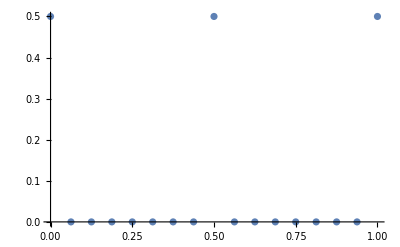

```mathematica
(*Medidas*)
Subscript[P, 0]={{1,0},{0,0}};
Subscript[P, 1]={{0,0},{0,1}};
For[i=0,i<32,i++,sub0=Mod[i,2];sub1=Which[i==0,0,Mod[i,2]==0&&sub1==0,1,Mod[i,2]==0&&sub1==1,0,True,sub1];sub2=Which[i==0,0,Mod[i,2^2]==0&&sub2==0,1,Mod[i,2^2]==0&&sub2==1,0,True,sub2];sub3=Which[i==0,0,Mod[i,2^3]==0&&sub3==0,1,Mod[i,2^3]==0&&sub3==1,0,True,sub3];Subscript[ψt, i]=N[KroneckerProduct[Subscript[P, sub3],Subscript[P, sub2],Subscript[P, sub1],Subscript[P, sub0],Id,Id,Id,Id].ketpsi];Subscript[ψt, i]=N[ConjugateTranspose[Subscript[ψt, i]].Subscript[ψt, i]];]

(*Organizar resultados de las medidas y graficar*)
L=Table[{i,i/2^4,Subscript[ψt, i][[1,1]]},{i,0,31}];
ListPlot[Table[{N[i/2^4],Subscript[ψt, i][[1,1]]},{i,0,16}],PlotRange->All]
```

```mathematica
M=8;
x=3;
L1=Table[{Denominator[FromContinuedFraction[ContinuedFraction[Transpose[L][[2,i]]]]],L[[i,3]]},{i,1,16}];
For[i=1,i≤Dimensions[L1][[1]],i++,For[j=1,j≤Dimensions[L1][[1]],j++,If[L1[[i,1]]==L1[[j,1]]&&i≠j,L1[[i,2]]+=L1[[j,2]];L1=Drop[L1,{j}];]]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[OddQ[L1[[i,1]]],L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[Mod[x^L1[[i,1]],M]≠1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,If[GCD[x^(L1[[1,1]]/2),M]==M-1,L1=Drop[L1,{i}];]]
For[i=1,i≤Dimensions[L1][[1]],i++,L1[[i,2]]=L1[[i,2]]/Sum[L1[[j,2]],{j,1,Dimensions[L1][[1]]}];]
L2=Table[{GCD[x^(L1[[i,1]]/2)+1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
L3=Table[{GCD[x^(L1[[i,1]]/2)-1,M],L1[[i,2]]},{i,1,Dimensions[L1][[1]]}];
```

{{16,1.99793×10^-27+0. ⅈ},{8,5.12056×10^-28+0. ⅈ},{4,1.27532×10^-28+0. ⅈ},{2,1.+0. ⅈ}}

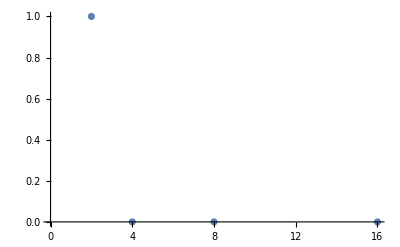

```mathematica
(*Graficar probabilidad de cada posible orden estimado*)
L1
ListPlot[L1]
```

{{2,1.99793×10^-27+0. ⅈ},{2,5.12056×10^-28+0. ⅈ},{2,1.27532×10^-28+0. ⅈ},{4,1.+0. ⅈ}}

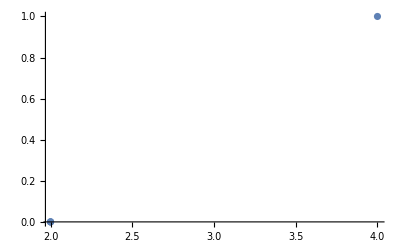

{{8,1.99793×10^-27+0. ⅈ},{8,5.12056×10^-28+0. ⅈ},{8,1.27532×10^-28+0. ⅈ},{2,1.+0. ⅈ}}

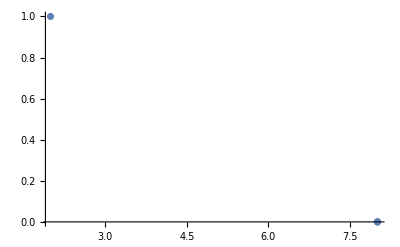

```mathematica
L2
ListPlot[L2]
L3
ListPlot[L3]
```